# 2014 Belediye Seçim Analizi

### Verilerin yüklenmesi

Mathematica doğrudan CSV yükleyebiliyor.

```mathematica
ankara=Import[FileNameJoin[{NotebookDirectory[],"..","ankara","ankara31mart2014.csv"}]];
istanbul=Import[FileNameJoin[{NotebookDirectory[],"..","istanbul","istanbul31mart2014.csv"}]];
```

### Pre-processing

```mathematica
analizSehriAnkara=True; (* Istanbul için False *)
{a0,sehir}=If[analizSehriAnkara,{ankara,"Ankara"},{istanbul,"İstanbul"}];
a=Join[
a0[[2;;All,1;;7]]ᵀ,
N[a0[[2;;All,8;;All]]]ᵀ
]ᵀ;
{il,ilce,sandik,alan,datevalue,timevalue,url,kayitli,kullanan,kanun,toplam,itirazsiz,itirazli,gecerlioy,gecersizoy,dspoy,dypoy,turkoy,hkpoy,bbpoy,akpoy,dpoy,mpoy,spoy,ldpoy,btpoy,hdpoy,chpoy,mhpoy,yurtpoy,ipoy,hakparoy,heparoy,gpoy,tkpoy,odpoy,apoy,bdpoy,mypoy,emepoy,hudaparoy}=aᵀ;
```

Oranları da bir hesaplayalım:

```mathematica
katilim=kullanan/kayitli;
akporan=akpoy/toplam;
chporan=chpoy/toplam;
mhporan=mhpoy/toplam;
hdporan=hdpoy/toplam;
indexes=Range[1,Length[a]];
alanindexes=GatherBy[indexes,{ilce[[#]],alan[[#]]}&];
alanboylari=Length/@alanindexes;
buyukalan=Select[alanindexes,Length[#]>10&];
```

### Seçim parmakizi

Seçim parmakizi fikrinin açıklaması için bkz. "Statistical detection of systematic election irregularities" (Klimek et al., 2012)

```mathematica
jet=Import[FileNameJoin[{NotebookDirectory[],"jet.mat"}],"Table"];
{jetr,jetg,jetb}=Interpolation[jet[[All,#]]]&/@{1,2,3};
jetf[x_]:=RGBColor[jetr[1+999x],jetg[1+999x],jetb[1+999x]];
```

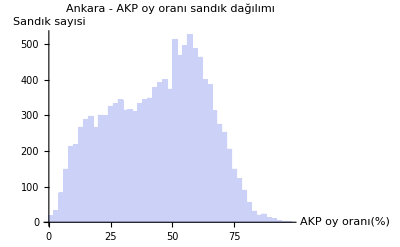

```mathematica
Histogram[
100akporan,
PlotLabel->sehir<>" - AKP oy oranı sandık dağılımı",
AxesLabel->{"AKP oy oranı(%)","Sandık sayısi"}
]
```

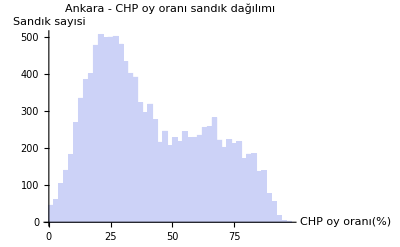

```mathematica
Histogram[
100chporan,
PlotLabel->sehir<>" - CHP oy oranı sandık dağılımı",
AxesLabel->{"CHP oy oranı(%)","Sandık sayısi"}
]
```

```mathematica
katilimMin=Min[1,#]&/@katilim;
```

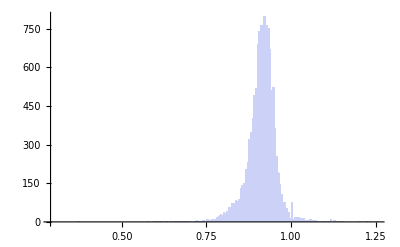

```mathematica
Histogram[katilim]
```

```mathematica
Quantile[katilim,0.01]//N
```

0.788462

```mathematica
parmakizi=BinCounts[{akporan,katilim}ᵀ,{0,1.0,0.01},{0.00,1.0,0.01}];
```

```mathematica
Legended[
ArrayPlot[
Reverse[parmakizi],
ColorFunction->jetf,
PlotLabel->"AKP oy oranı ve katılım'a göre sandık sayısı - "<>sehir<>" 2014",
GridLines->Automatic,
FrameTicks->{Range[0,100,10]},
DataReversed->False,
DataRange->{{0,100},{0,100}}
],
BarLegend[{jetf[#/Max[parmakizi]]&,{0,Max[parmakizi]}},10,LegendLabel->"Sandık sayısı"]
]
```

-Graphics-

```mathematica
akpord=Ordering[akpoy];
katilimord=Ordering[katilim];
```

```mathematica
Histogram[katilim]
```

-Graphics-

```mathematica
goster[u_]:=
Legended[
ArrayPlot[
u,
ColorFunction->jetf,
PlotLabel->"",
GridLines->Automatic,
FrameTicks->{Range[0,100,10]},
DataReversed->False,
DataRange->{{0,100},{0,100}}
],
BarLegend[{jetf[(#-Min[u])/(Max[u]-Min[u])]&,{Min[u],Max[u]}},10,
LegendLabel->"?"]
]
```

```mathematica
goster[
ArrayReshape[katilim[[katilimord]],{110,111},Max[katilim]]
]
```

-Graphics-

```mathematica
goster[
GaussianFilter[
ArrayReshape[chpoy[[katilimord]],{110,111},Max[katilim]],0.1]
]
```

-Graphics-

### Logarithmic vote rate

```mathematica
akpoynz=Select[indexes,akpoy[[#]]>0&&kayitli[[#]]>akpoy[[#]]&];
logvr=N[Log[(kayitli-akpoy)[[akpoynz]]/akpoy[[akpoynz]]]];
μlogvr=Mean[logvr];
σlogvr=StandardDeviation[logvr];
logvrs=(logvr-μlogvr)/σlogvr;
```

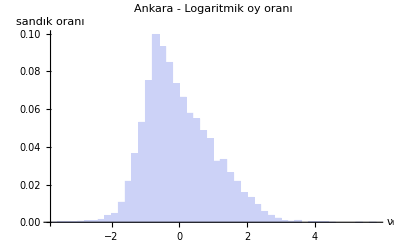

```mathematica
Histogram[logvrs,Automatic,"Probability",
PlotLabel->sehir<>" - Logaritmik oy oranı",
AxesLabel->{"ν_i","sandık oranı"}]
```

### Cumulative winner votes vs. turnout

```mathematica
akpoycum=Accumulate[akpoy[[katilimord]]];
```

```mathematica
toplamoy=N[Total[toplam]]
```

3.28385×10^6

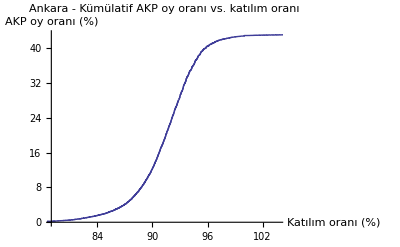

```mathematica
ListPlot[
{100katilim[[katilimord]],100akpoycum/toplamoy}ᵀ,Joined->True,
PlotLegends->{""},
AxesLabel->{"Katılım oranı (%)","AKP oy oranı (%)"},
PlotLabel->sehir<>" - Kümülatif AKP oy oranı vs. katılım oranı"
]
```

### AKP vs CHP neighbourhoods

First, gather votes by polling station:

```mathematica
aalan=GatherBy[a,#[[4]]&];
aalant=Function[a,Join[a[[1,1;;7]],Total[a[[All,8;;]]]]]/@aalan;
{ilA,ilceA,sandikA,alanA,datevalueA,timevalueA,urlA,kayitliA,kullananA,kanunA,toplamA,itirazsizA,itirazliA,gecerlioyA,gecersizoyA,dspoyA,dypoyA,turkoyA,hkpoyA,bbpoyA,akpoyA,dpoyA,mpoyA,spoyA,ldpoyA,btpoyA,hdpoyA,chpoyA,mhpoyA,yurtpoyA,ipoyA,hakparoyA,heparoyA,gpoyA,tkpoyA,odpoyA,apoyA,bdpoyA,mypoyA,emepoyA,hudaparoyA}=aalantᵀ;
katilimA=kullananA/kayitliA;
katilimAord=Ordering[katilimA];
akpoyAcum=Accumulate[akpoyA[[katilimAord]]];
chpoyAcum=Accumulate[chpoyA[[katilimAord]]];
akpchpoyfarkAcum=Accumulate[(akpoyA-chpoyA)[[katilimAord]]];
toplamoy=N[Total[toplam]]
```

3.28385×10^6

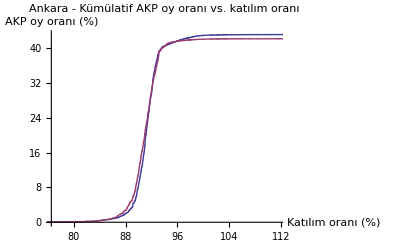

```mathematica
ListPlot[
{
{100katilimA[[katilimAord]],100akpoyAcum/toplamoy}ᵀ,
{100katilimA[[katilimAord]],100chpoyAcum/toplamoy}ᵀ
},Joined->True,
PlotLegends->{""},
AxesLabel->{"Katılım oranı (%)","AKP oy oranı (%)"},
PlotLabel->sehir<>" - Kümülatif AKP oy oranı vs. katılım oranı"
]
```

```mathematica
indexesA=Range[1,Length[aalant]];
katilimG=GatherBy[indexesA,katilimA[[#]]&];
akpoyB=(Total[akpoyA[[#]]]/toplamoy)&/@katilimG;
chpoyB=(Total[chpoyA[[#]]]/toplamoy)&/@katilimG;
katilimB=
(Total[kullananA[[#]]]/Total[kayitliA[[#]]])&/@katilimG;
katilimBo=Ordering[katilimB];
```

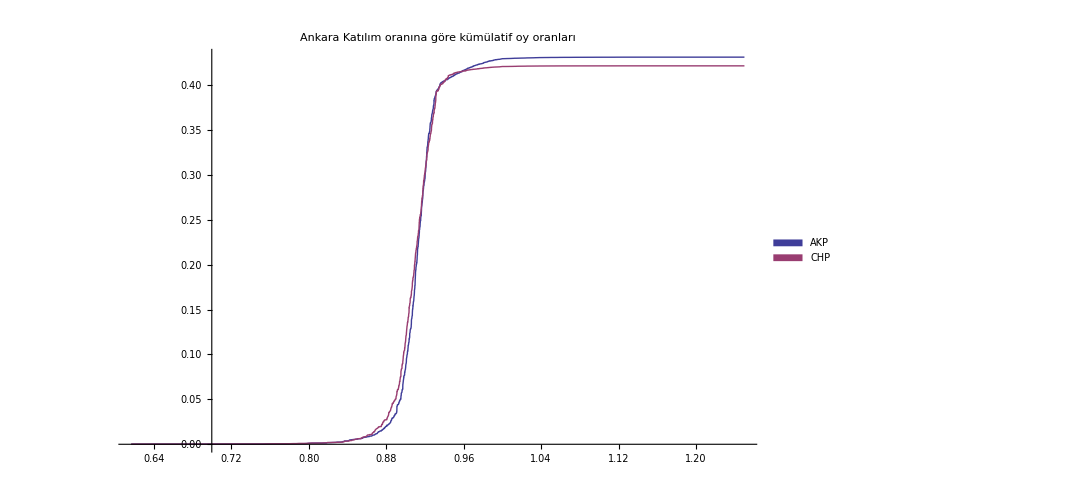

```mathematica
x=ListPlot[
{
{katilimB[[katilimBo]],Accumulate[akpoyB[[katilimBo]]]}ᵀ,
{katilimB[[katilimBo]],Accumulate[chpoyB[[katilimBo]]]}ᵀ
},
PlotRange->Full,
PlotLabel->sehir<>"\nKatılım oranına göre kümülatif oy oranları",
PlotLegends->SwatchLegend[{"AKP","CHP"},LabelStyle->{FontFamily->"Sans"}],
Joined->True,
ImageSize->800
]
```

```mathematica
akpcum={katilimB[[katilimBo]],Accumulate[akpoyB[[katilimBo]]]}ᵀ;
akpcumga=GatherBy[akpcum,Round[#[[1]],0.001]&];
akpcumgam={#[[1,1]],Mean[#[[All,2]]]}&/@akpcumga;
akpcumgamf=Interpolation[akpcumgam,InterpolationOrder->1];
```

```mathematica
chpcum={katilimB[[katilimBo]],Accumulate[chpoyB[[katilimBo]]]}ᵀ;
chpcumga=GatherBy[chpcum,Round[#[[1]],0.001]&];
chpcumgam={#[[1,1]],Mean[#[[All,2]]]}&/@chpcumga;
chpcumgamf=Interpolation[chpcumgam,InterpolationOrder->1];
```

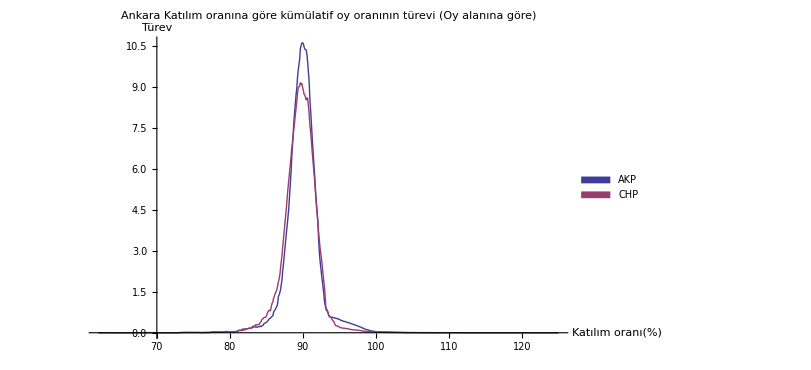

```mathematica
p=Plot[
{
(*akpcumgamf[x],
chpcumgamf[x],*)
((akpcumgamf[x/100+0.025]-akpcumgamf[x/100])/0.025),
((chpcumgamf[x/100+0.025]-chpcumgamf[x/100])/0.025)
},
{x,62,125},
PlotRange->Full,
PlotLabel->sehir<>"\nKatılım oranına göre\nkümülatif oy oranının türevi\n(Oy alanına göre)",
AxesLabel->{"Katılım oranı(%)","Türev"},
PlotLegends->SwatchLegend[{"AKP","CHP"},LabelStyle->{FontFamily->"Sans"}],
LabelStyle->{FontFamily->"Sans"},
ImageSize->600
]
```

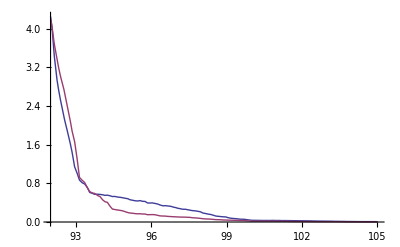

```mathematica
p=Plot[
{
(*akpcumgamf[x],
chpcumgamf[x],*)
((akpcumgamf[x/100+0.025]-akpcumgamf[x/100])/0.025),
((chpcumgamf[x/100+0.025]-chpcumgamf[x/100])/0.025)
},
{x,92,105},
PlotRange->Full,
(*PlotLabel->sehir<>"\nKatılım oranına göre\nkümülatif oy sayısının türevi (detay)\n(Oy alanına göre)",
AxesLabel->{"Katılım oranı(%)","Türev"},*)
(*PlotLegends->SwatchLegend[{"AKP","CHP"},LabelStyle->{FontFamily->"Sans"}],
LabelStyle->{FontFamily->"Sans"},*)
ImageSize->400
]
```